Solving 2-D Poisson Equation for Structure B (500V)...

⟶ Oxide voltage share under the drain: 53.9%

Generating 3-D Potential Surface...

Generating 2-D Map and 1-D Cross-Section...

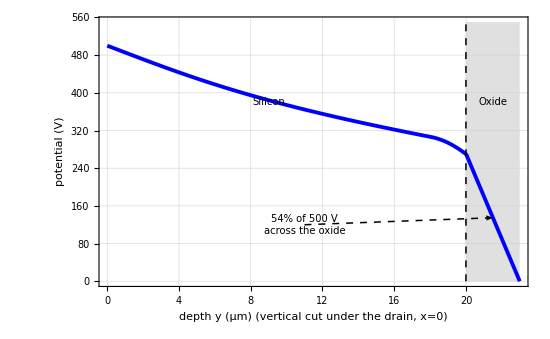
-Graphics3D-
-Graphics-
-Graphics-

```mathematica
(* ::Package::*)(* =========================================================================*)(*1. Physical Constants& Device Geometry*)(* =========================================================================*)q=1.60217662*^-19;      (*Elementary charge (C)*)
eps0=8.854187817*^-14;  (*Vacuum permittivity (F/cm)*)
epsSi=11.7*eps0;      (*Silicon permittivity*)
epsOx=3.9*eps0;       (*Oxide permittivity*)
um=1.0*^-4;             (*Micrometer to cm conversion*)

(*Device Parameters (Structure B)*)
Lx=50.0*um;           (*Total width*)
Lsi=20.0*um;          (*Silicon thickness*)
tox=3.0*um;           (*Oxide thickness*)
H=Lsi+tox;            (*Total depth*)
wn=2.0*um;            (*Shallow n-layer thickness*)
ND0=1.0*^14;            (*Background doping (cm^-3)*)
SD=1.5*^12;             (*Shallow layer dose (cm^-2)*)
drainW=8.0*um;        (*Drain width*)
sourceW=8.0*um;       (*Source width*)
Vapplied=500.0;         (*Applied drain voltage*)

(* =========================================================================*)
(*2. Material& Charge Definitions*)
(* =========================================================================*)
(*Permittivity map*)
eps[y_]:=Piecewise[{{epsSi,y<=Lsi},{epsOx,y>Lsi}}];

(*Net charge density ρ=q*N_net (C/cm^3)*)
rho[y_]:=Piecewise[{{q*(ND0+SD/wn),Lsi-wn<=y<=Lsi},(*Shallow N-layer*){q*ND0,0<=y<Lsi-wn}                 (*Bulk N-drift region*)},0];                                           (*Oxide is charge-free*)

(* =========================================================================*)
(*3. PDE Setup& FEM Solve*)
(* =========================================================================*)
Print["Solving 2-D Poisson Equation for Structure B (500V)..."];

(*Governing PDE:∇·(ε∇ϕ)=-ρ*)
pde=Inactive[Div][-eps[y]*Inactive[Grad][phi[x,y],{x,y}],{x,y}]==rho[y];

(*Boundary Conditions (Structure B)*)
bcs={DirichletCondition[phi[x,y]==0,y==H],(*Substrate grounded*)DirichletCondition[phi[x,y]==Vapplied,y==0&&x<=drainW],(*Drain at 500V*)DirichletCondition[phi[x,y]==0,y==0&&x>=Lx-sourceW],(*Source grounded*)DirichletCondition[phi[x,y]==0,x==Lx&&y<=Lsi]               (*p+sinker grounded*)};

(*Solve using NDSolveValue*)
phiSolution=NDSolveValue[{pde,bcs},phi,{x,0,Lx},{y,0,H},Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->(Lx*H)/25000}}}];

(*Calculate quantitative metrics*)
vDrainBottom=phiSolution[0,Lsi];
oxideShare=vDrainBottom/Vapplied;
Print["⟶ Oxide voltage share under the drain: ",Round[oxideShare*100,0.1],"%"];

(* =========================================================================*)
(*4. 3-D Wireframe Plot (Fig.4 reproduction)*)
(* =========================================================================*)
Print["Generating 3-D Potential Surface..."];
fig3D=Plot3D[phiSolution[x*um,y*um],{x,0,Lx/um},{y,0,H/um},ColorFunction->"Rainbow",Mesh->{45,60},MeshStyle->Directive[Black,Thickness[0.001]],PlotStyle->Directive[Opacity[0.95]],PlotPoints->100,ScalingFunctions->{Identity,"Reverse",Identity},(*Invert depth axis*)AxesLabel->{"x (μm)","depth y (μm)","potential (V)"},PlotLabel->Style["Fig.4 Potential distribution — 3-D view",12,Bold],ViewPoint->{-2,-2.5,1.5},ImageSize->600,Epilog->{Inset[Style["oxide film",10,Black],Scaled[{0.15,0.2}]],Inset[Style["n layer (500 V)",10,Black],Scaled[{0.2,0.85}]],Inset[Style["p+ layer (0 V)",10,Black],Scaled[{0.85,0.85}]]}];

(* =========================================================================*)
(*5. 2-D Contour Plot& 1-D Vertical Cut*)
(* =========================================================================*)
Print["Generating 2-D Map and 1-D Cross-Section..."];

fig2DMap=ContourPlot[phiSolution[x*um,y*um],{x,0,Lx/um},{y,0,H/um},Contours->Range[0,Vapplied,25],ColorFunction->"Rainbow",ContourStyle->Directive[Black,Thickness[0.002]],PlotPoints->100,ScalingFunctions->{Identity,"Reverse"},FrameLabel->{"x (μm)","depth y (μm)"},PlotLabel->Style["Fig.4 Potential distribution — 2-D map",11,Bold],PlotLegends->BarLegend[Automatic,LegendLabel->"potential (V)"],Epilog->{White,Thickness[0.005],Dashed,Line[{{0,Lsi/um},{Lx/um,Lsi/um}}],Text[Style["buried oxide",10,White],{25,21.5}],Text[Style["drain 500 V",10,Bold,White],{4,2}],Text[Style["source 0 V",10,Bold,White],{40,2}]},ImageSize->550];

fig1DCut=Plot[phiSolution[0,y*um],{y,0,H/um},PlotStyle->Directive[Blue,Thickness[0.005]],PlotRange->{{0,H/um},{0,Vapplied+50}},Frame->True,FrameLabel->{"depth y (μm)   (vertical cut under the drain, x=0)","potential (V)"},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.8],Dashed],Prolog->{GrayLevel[0.8,0.6],Rectangle[{Lsi/um,0},{H/um,Vapplied+50}]},Epilog->{Black,Dashed,Thickness[0.002],Line[{{Lsi/um,0},{Lsi/um,Vapplied+50}}],Text[Style["Silicon",10],{9,380}],Text[Style["Oxide",10],{21.5,380}],Text[Style[ToString[Round[oxideShare*100]]<>"% of 500 V\nacross the oxide",10],{11,120}],Arrow[{{11,120},{21.5,vDrainBottom/2}}]},ImageSize->550];

(* =========================================================================*)
(*6. Display Output*)
(* =========================================================================*)
Column[{fig3D,fig2DMap,fig1DCut},Alignment->Center,Spacings->2]
```